# Equilibrium calculations for the hiring dynamics model Last updated: March 28, 2020 Mari Kawakatsu (Note: we can eventually turn everything into a function. For now this is just scratch work.)

## Base case: n = 2

Let' s define the base variables first:

```mathematica
n=2;(*no. of agents*)
ve=ConstantArray[1,n]; (*vector of ones*)
vzero=ConstantArray[0,n];
```

Next, define the derived variables :

```mathematica
Dout[AA_]:=DiagonalMatrix[Total[AA,{2}]]; (*row sum*)
Din[AA_]:=DiagonalMatrix[Total[AA,{1}]];(*col sum*)
L[AA_]:=Dout[AA]+Din[AA]-(AA+Transpose@AA) ;
Lα[AA_,α_]:=L[AA]+α *IdentityMatrix[n];
Λ[AA_]:=Dout[AA]-Din[AA];
```

```mathematica
γ[SS_,β_]:=Exp[β*SS]/Total[Exp[β*SS]];(*normalize*)
G[SS_,β_]:=Table[γ[SS,β],n];(*each of n rows is a copy of γ*)
```

Finally, let's define the variables that we only need in expectation:

```mathematica
EΔ[SS_,β_]:=1/n G[SS,β];
EδΛ[AA_,SS_,β_,λ_]:=(λ-1)(Λ[AA]+DiagonalMatrix[EΔ[SS,β].ve-Transpose@EΔ[SS,β].ve])
ELΔ[SS_,β_]:=DiagonalMatrix[EΔ[SS,β].ve+Transpose@EΔ[SS,β].ve]-EΔ[SS,β]-Transpose@EΔ[SS,β]
EδL[AA_,SS_,β_,λ_]:=(λ-1)(L[AA]-ELΔ[SS,β])
```

We want to solve the equation F(s) = 0.  The most general case is

```mathematica
A=Array[a,{n,n}];(*adjacenty matrix*)
S=Array[s,n];(*SpringRank vector*)
```

Just to confirm that these are what we want:

```mathematica
A //MatrixForm
S // MatrixForm
```

(a[1,1] | a[1,2]
a[2,1] | a[2,2])

(s[1]
s[2])

```mathematica
(*Λ[A].ve // MatrixForm*)
L[A] // MatrixForm
(*EΔ[S,β] // MatrixForm*)
ELΔ[S,β] // MatrixForm
(*EδΛ[A,S,β,λ].ve //FullSimplify// MatrixForm*)
EδL[A,S,β,λ]// FullSimplify// MatrixForm
```

(a[1,2]+a[2,1] | -a[1,2]-a[2,1]
-a[1,2]-a[2,1] | a[1,2]+a[2,1])

(ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))+ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2]))) | -ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))-ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))
-ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))-ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2]))) | ⅇ^(β s[1])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2])))+ⅇ^(β s[2])/(2 (ⅇ^(β s[1])+ⅇ^(β s[2]))))

(1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1]) | -1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1])
-1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1]) | 1/2 (-1+λ) (-1+2 a[1,2]+2 a[2,1]))

```mathematica
S=FullSimplify[Inverse[Lα[A,α]].Λ[A].ve];
S // MatrixForm
S[[1]] // FullSimplify
(*S[[1]]-S[[2]] // FullSimplify*)
```

((a[1,2]-a[2,1])/(α+2 (a[1,2]+a[2,1]))
(-a[1,2]+a[2,1])/(α+2 (a[1,2]+a[2,1])))

(a[1,2]-a[2,1])/(α+2 (a[1,2]+a[2,1]))

```mathematica
EδΛ[A,S,β,λ].ve-EδL[A,S,β,λ].S // FullSimplify  // MatrixForm
```

(1/2 (-1+λ) ((2 (1+α) (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))-Tanh[(β (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))])
1/2 (-1+λ) (-(2 (1+α) (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))+Tanh[(β (a[1,2]-a[2,1]))/(α+2 (a[1,2]+a[2,1]))]))

```mathematica
(*Let (a[1,2]+a[2,1])=1/2 and also divide what's inside the last set of parentheses by 2*)
sol = FindRoot[((((1+α)x)/(α+2 (1/2))-1/2 Tanh[(β x)/(α+2 (1/2))])/.{α->10^-15,β->3})==0,{x,0.5}] ;
NumberForm[sol,8]
NumberForm[(x/(1/2(α+2)))/.{α->10^-15} /.sol,8]
```

{x→0.42927982}

0.42927982

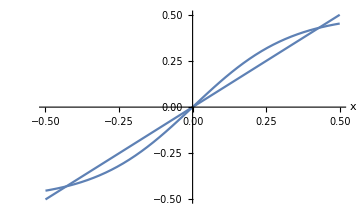

```mathematica
Plot[{((1+α) x)/((1/2)(α+2)),1/2 Tanh[(β x)/((1/2)(α+2))]}/.{α->10^-15,β->3},{x,-0.5,0.5},AxesLabel->Automatic,ImageSize->Medium]
```

## Generalization: n > 2

```mathematica
Clear[n]
```

Let n_1and n_2be the number of agents / departments with SpringRank scores s_1and s_2, respectively, with n_1+n_2=n.  The rows corresponding to agents with the same scores will be identical, and all elements within each row will be identical:

```mathematica
n1=7;n2=3;
n=n1+n2;
ve=ConstantArray[1,n]; (*vector of ones*)
vzero=ConstantArray[0,n];
```

```mathematica
A=Join[ConstantArray[a,{n1,n}],ConstantArray[b,{n2,n}],1];(*adjacenty matrix*)
S=FullSimplify[Inverse[Lα[A,α]].Λ[A].ve];
Cond=EδΛ[A,S,β,λ].ve-EδL[A,S,β,λ].S // FullSimplify;
Cond //MatrixForm;
```

```mathematica
sol=FindRoot[(Cond[[1]]/(-1+λ)/.{b->(1/n-a n1)/n2,α->10^-15,β->3} ),{a,0}]
Ssol=S/.{b->1/n2(1/n-a*n1),α->10^-15,β->3}/.sol
```

{a→0.00215421}

{-0.257568,-0.257568,-0.257568,-0.257568,-0.257568,-0.257568,-0.257568,0.600992,0.600992,0.600992}